### Copy Drees formula

```mathematica
FF[x_]:=30/(7 Pi^4)NIntegrate[((4 y^2-x^2)√(y^2-x^2))/(Exp[y]+1),{y,x,Infinity}]
FB[x_]:=30/(7 Pi^4)NIntegrate[((4 y^2-x^2)√(y^2-x^2))/(Exp[y]-1),{y,x,Infinity}]
```

```mathematica
Nnu=3;TnuD=2.3;
```

### Reproduce Drees results

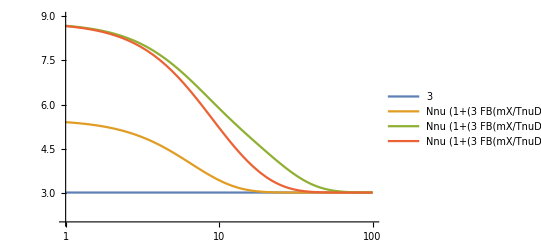

```mathematica
LogLinearPlot[{3,Nnu(1+1/Nnu 3/2 FB[mX/TnuD])^(4/3), Nnu(1+1/Nnu 3/2 FB[mX/TnuD]+1/Nnu 4/2 FF[(0.31 mX)/TnuD])^(4/3),Nnu(1+1/Nnu 3/2 FB[mX/TnuD]+1/Nnu 4/2 FF[(0.51 mX)/TnuD])^(4/3)},{mX,1,100},PlotLegends->"Expressions",PlotRange->{2,9}]
```

Agrees well with Figure 2 in Drees paper